#### 091818New Calibration trace at YOKO=0mA, 6.45~6.6GHz, 5dBm 10us integration 250Kavg,100KHz step

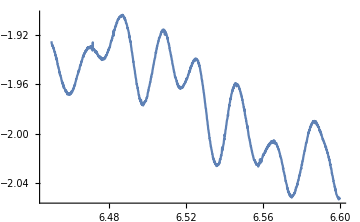
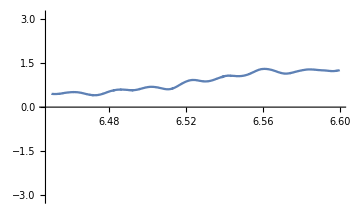

```mathematica
file=(*"E:\\Data\\fluxonium waveguide\\one_tone_6.45GHz_to_6.6GHz_5dBm_0mA_10us integration_200Kavg_100KHz step_091918.dat";*)
"D:\\Travail Nath\\JQI\\Original Data and analysis\\Original data\\one_tone_6.45GHz_to_6.6GHz_5dBm_0mA_10us integration_200Kavg_100KHz step_091918.dat";
data=Import[file];
header=Take[data,1];
ref=Drop[data,1];
edelay = 322.0;
ampref=ref[[;;,3]];
phaseref=ref[[;;,2]];
powerRef = 5;
Row@{ListLinePlot[{#[[1]],Log10@#[[3]]}&/@ref,PlotRange->All,ImageSize->Medium],
ListLinePlot[{#[[1]],Arg[Exp[I(#[[2]]-edelay*#[[1]])]]}&/@ref,PlotRange->{-Pi,Pi},ImageSize->Medium]}
```

## Plot the circles (contains different fits, you can focus on the options for the plots only if you want)

```mathematica
file=(*"E:\\Data\\fluxonium waveguide\\100218_no pump_one_tone_6.48GHz_to_6.495GHz_-25dBm_to_-10dBm_-0.575mA_integration 3us_ 200Kavg_30us blank.dat";*)
"D:\\Travail Nath\\JQI\\Original Data and analysis\\Original data\\100218_no pump_one_tone_6.48GHz_to_6.495GHz_-25dBm_to_-10dBm_-0.575mA_integration 3us_ 200Kavg_30us blank.dat";
data=Import[file];
header=Take[data,1]
data=Drop[data,1];
edelay = 322;
phaseoffset=-0.4π/2;
npoints=Length[Select[data,#[[1]]==data[[1,1]]&]];
startFreq=6.48;
stopFreq=6.495;
stepFreq=0.0001;
npower=7;
start=IntegerPart[1+(startFreq-6.45)/stepFreq];
stop=IntegerPart[1+(stopFreq-6.45)/stepFreq];
freq=data[[;;npoints,2]];
nfreq=Length[freq];
amp=Table[data[[1+(i-1)*npoints;;i*npoints,4]],{i,1,npower}];
phase=Table[data[[1+(i-1)*npoints;;i*npoints,3]],{i,1,npower}];
power=data[[1;;;;npoints,1]];
phaseoffset=-0.4π/2;
refl=Table[10^(-(power[[i]]-powerRef)/20)*amp[[i,j]]/ampref[[start+(j-1)]]*Exp[I*(phase[[i,j]]-edelay*freq[[j]]+phaseoffset)],{j,1,nfreq},{i,1,npower}];
Clear[p,s,f,f0,Γ,P,α,d];
tofit=Table[{freq[[j]],10^((power[[k]]-powerRef)/10),l,l*Im@refl[[j,k]]+(1-l)*Re@refl[[j,k]]},{k,1,npower},{l,0,1},{j,1,nfreq}];
tofit2=Table[{freq[[j]],10^((power[[k]]-powerRef)/10),l,l*Im@refl[[j,k]]+(1-l)*Re@refl[[j,k]]},{k,1,npower},{l,0,1},{j,1,151}];
fit=FindFit[Flatten[tofit2,2],(1-s)*Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α   P)]+s*Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α P)],{{f0,(freq[[1]]+freq[[-1]])/2},{Γ,0.006},{p,0.6},{α,0.003}},{f,P,s}]
Show[ListPlot[Table[Transpose@{tofit[[i,1,;;,-1]],tofit[[i,2,;;,-1]]},{i,1,npower}],PlotRange->{{-0.3,1.1},{-0.7,0.7}},AspectRatio->1, PlotMarkers->{"●"},LabelStyle->{FontSize->20}],Table[
ParametricPlot[{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α ( tofit[[i,1,1,2]]))],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α (tofit[[i,1,1,2]]))]}/.fit,{f,5,8},PlotStyle->Red,PlotPoints->400],{i,1,npower}]]
```

{{power,freq,demod_Phase0,demod_Magnitude0}}

{f0→6.48775,Γ→0.00261675,p→0.534501,α→0.000489422}

-Graphics-

{f0→6.48774,Γ→0.00261743,p→0.534758,α→0.000490403}

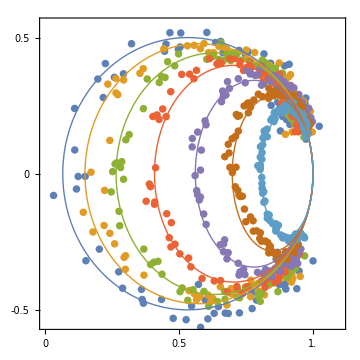

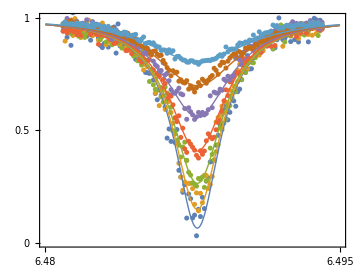

```mathematica
npower=7;
start=IntegerPart[1+(startFreq-6.45)/stepFreq];
stop=IntegerPart[1+(stopFreq-6.45)/stepFreq];
freq=data[[;;npoints,2]];
nfreq=Length[freq];
amp=Table[data[[1+(i-1)*npoints;;i*npoints,4]],{i,1,npower}];
phase=Table[data[[1+(i-1)*npoints;;i*npoints,3]],{i,1,npower}];
power=data[[1;;;;npoints,1]];
phaseoffset=-0.39π/2;
refl=Table[10^(-(power[[i]]-powerRef)/20)*amp[[i,j]]/ampref[[start+(j-1)]]*Exp[I*(phase[[i,j]]-edelay*freq[[j]]+phaseoffset)],{j,1,nfreq},{i,1,npower}];
Clear[p,s,f,f0,Γ,P,α,d];
tofit=Table[{freq[[j]],10^((power[[k]]-powerRef)/10),l,l*Im@refl[[j,k]]+(1-l)*Re@refl[[j,k]]},{k,1,npower},{l,0,1},{j,1,nfreq}];
tofit2=Table[{freq[[j]],10^((power[[k]]-powerRef)/10),l,l*Im@refl[[j,k]]+(1-l)*Re@refl[[j,k]]},{k,1,npower},{l,0,1},{j,1,151}];
fit=FindFit[Flatten[tofit2,2],(1-s)*Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α   P)]+s*Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α P)],{{f0,(freq[[1]]+freq[[-1]])/2},{Γ,0.006},{p,0.6},{α,0.003}},{f,P,s}]
PlotIndices={1,2,3,4,5,6,7};
Show[ListPlot[Table[Transpose@{tofit[[i,1,10;;-30,-1]],tofit[[i,2,10;;-30,-1]]},{i,PlotIndices}],PlotRange->{{0,1.1},{-0.55,0.55}},AspectRatio->1,PlotStyle->PointSize[0.015]],
ParametricPlot[Evaluate@Table[{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]}/.fit,{i,PlotIndices}],{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Thick],Frame->True,FrameTicks->{{{-0.5,0,0.5},None},{{0,0.5,1.0},None}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
Show[ListPlot[Table[Transpose@{tofit[[i,1,10;;-10,-4]],tofit[[i,1,10;;-10,-1]]},{i,PlotIndices}],PlotStyle->PointSize[0.01],PlotRange->{{6.48,6.495},{0,1}}],Plot[Evaluate@Table[Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]/.fit,{i,PlotIndices}],{f,6.48,6.495},PlotRange->All,PlotStyle->Thick],Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{Table[6.48+0.005i,{i,0,10}],None}},FrameTicksStyle->Directive[Black,16],AspectRatio->0.75,ImageSize->Medium]
(*Show[ListPlot[Table[Transpose@{tofit[[i,1,10;;-90,-4]],tofit[[i,2,10;;-90,-1]]},{i,PlotIndices}],PlotStyle->PointSize[0.01],PlotRange->{{6.48,6.495},{0,1}}],Plot[Evaluate@Table[Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]/.fit,{i,PlotIndices}],{f,6.48,6.495},PlotRange->All,PlotStyle->Thick],Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{Table[7.13+0.005i,{i,0,10}],None}},FrameTicksStyle->Directive[Black,16],AspectRatio->0.75,ImageSize->Medium]*)
```

```mathematica
power
```

{-25.,-22.5,-20.,-17.5,-15.,-12.5,-10.}

```mathematica
ΩRabi =10^3 √(α 10^((power-powerRef)/10))/.fit
```

{0.700288,0.933849,1.24531,1.66064,2.21451,2.95309,3.93801}

```mathematica
ΩRabi
```

{0.700288,0.933849,1.24531,1.66064,2.21451,2.95309,3.93801}

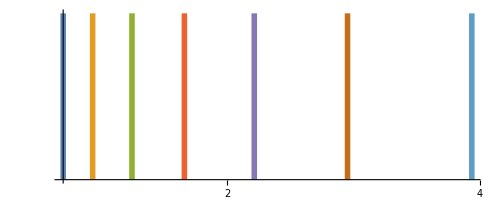

```mathematica
ParametricPlot[Evaluate[{#,x}&/@ΩRabi],{x,-0,0.5},PlotStyle->Thickness[0.01],Ticks->{Table[i,{i,0,10}],None},TicksStyle->Directive[Black,"Arial", 14]]
```

{f0→6.48774,Γ→0.00261743,p→0.534758,α→0.000490403}

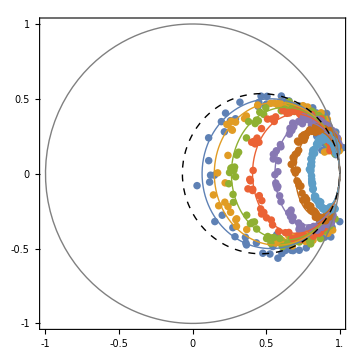

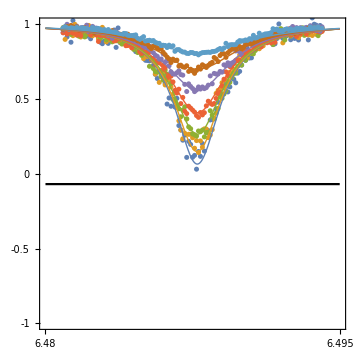

```mathematica
npower=7;
start=IntegerPart[1+(startFreq-6.45)/stepFreq];
stop=IntegerPart[1+(stopFreq-6.45)/stepFreq];
freq=data[[;;npoints,2]];
nfreq=Length[freq];
amp=Table[data[[1+(i-1)*npoints;;i*npoints,4]],{i,1,npower}];
phase=Table[data[[1+(i-1)*npoints;;i*npoints,3]],{i,1,npower}];
power=data[[1;;;;npoints,1]];
phaseoffset=-0.39π/2;
refl=Table[10^(-(power[[i]]-powerRef)/20)*amp[[i,j]]/ampref[[start+(j-1)]]*Exp[I*(phase[[i,j]]-edelay*freq[[j]]+phaseoffset)],{j,1,nfreq},{i,1,npower}];
Clear[p,s,f,f0,Γ,P,α,d];
tofit=Table[{freq[[j]],10^((power[[k]]-powerRef)/10),l,l*Im@refl[[j,k]]+(1-l)*Re@refl[[j,k]]},{k,1,npower},{l,0,1},{j,1,nfreq}];
tofit2=Table[{freq[[j]],10^((power[[k]]-powerRef)/10),l,l*Im@refl[[j,k]]+(1-l)*Re@refl[[j,k]]},{k,1,npower},{l,0,1},{j,1,151}];
fit=FindFit[Flatten[tofit2,2],(1-s)*Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α   P)]+s*Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α P)],{{f0,(freq[[1]]+freq[[-1]])/2},{Γ,0.006},{p,0.6},{α,0.003}},{f,P,s}]
PlotIndices={1,2,3,4,5,6,7};
Show[ListPlot[Table[Transpose@{tofit[[i,1,10;;-30,-1]],tofit[[i,2,10;;-30,-1]]},{i,PlotIndices}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->PointSize[0.015]],
ParametricPlot[Evaluate@Table[{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]}/.fit,{i,PlotIndices}],{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Thick],
ParametricPlot[Evaluate@{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Black,Thick,Dashed]],
ParametricPlot[Evaluate@{Re[1-(2 Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2  Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Gray,Thick]]
,Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{{-1,-0.5,0,0.5,1.0},None}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]


Show[ListPlot[Table[Transpose@{tofit[[i,1,10;;-10,-4]],tofit[[i,1,10;;-10,-1]]},{i,PlotIndices}],PlotStyle->PointSize[0.01],PlotRange->{{6.48,6.495},{-1,1}}],Plot[Evaluate@Table[Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]/.fit,{i,PlotIndices}],{f,6.48,6.495},PlotRange->All,PlotStyle->Thick],
Plot[1-2p/.fit,{f,6.48,6.495},PlotStyle->Black],Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{Table[6.48+0.005i,{i,0,10}],None}},FrameTicksStyle->Directive[Black,16],AspectRatio->1,ImageSize->Medium]
(*Show[ListPlot[Table[Transpose@{tofit[[i,1,10;;-90,-4]],tofit[[i,2,10;;-90,-1]]},{i,PlotIndices}],PlotStyle->PointSize[0.01],PlotRange->{{6.48,6.495},{0,1}}],Plot[Evaluate@Table[Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]/.fit,{i,PlotIndices}],{f,6.48,6.495},PlotRange->All,PlotStyle->Thick],Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{Table[7.13+0.005i,{i,0,10}],None}},FrameTicksStyle->Directive[Black,16],AspectRatio->0.75,ImageSize->Medium]*)
```